```mathematica
SetDirectory["E:\\MyMathMa\\liner\\img"]
```

E:\MyMathMa\liner\img

```mathematica
Clear[f,a,b,g];
g[f_,a_,b_]:=a f+b;
L=256;
```

```mathematica
a=-1;
b=L-1;
```

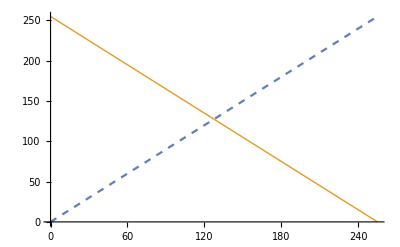

```mathematica
Plot[{f,g[f,a,b]},{f,0,L-1},PlotStyle->{Dashed,Thick}]
```

```mathematica
img = Import["lena_color_256.tif"];
d1=ImageData[img];
d2=1-d1;
img2=Image[d2];
img3=Import["lena_gray_256.tif"];
d3=ImageData[img3,"Byte"];
d4=L-1-d3;
img4=Image[d4,"Byte"];
Grid[{{img,img2,img3,img4}}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
img=Import["Fig0304(a)(breast_digital_Xray).tif"];
d=ImageData[img];
d2=1-d;
img2=Image[d2];
Grid[{{img,img2}}]
```

-Graphics- | -Graphics-

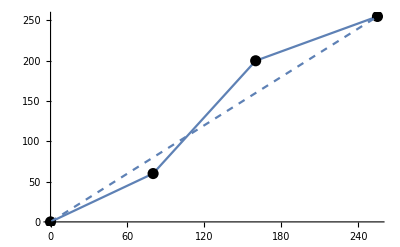

```mathematica
L=256;
p1={80,60};
p2={160,200};
g1=ListPlot[{{0,0},p1,p2,{L-1,L-1}},Joined->True];
ref=ListPlot[{{0,0},{L-1,L-1}},Joined->True,PlotStyle->Dashed];
g2=Graphics[{PointSize[0.02],Point[{{0,0},p1,p2,{255,255}}]}];
Show[g1,g2,ref]
```

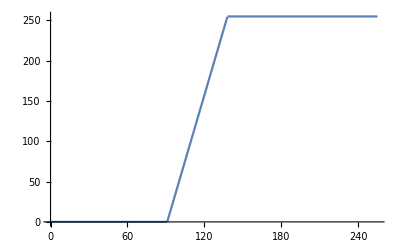

```mathematica
L=256;
img=Import["Fig0310(b)(washed_out_pollen_image).tif"];
d=ImageData[img,"Byte"];
min=Min[d];
max=Max[d];
line2point[x_,p1_,p2_]:=Module[{},(p2[[2]]-p1[[2]])/(p2[[1]]-p1[[1]])*(x-p1[[1]])+p1[[2]]];
piecePhrase[x_]=Module[{p1={min,0},p2={max,L-1}},Piecewise[{{0,x<=min},{line2point[x,p1,p2],p1[[1]]<x<p2[[1]]},{L-1,p2[[1]]<=x<=L-1}}]];
Plot[piecePhrase[x],{x,0,255}]
```

```mathematica
d2=Map[piecePhrase,d,{2}];
t=Round[d2];
img2=Image[t,"Byte"];
Grid[{{img,img2}}]
```

-Graphics- | -Graphics-

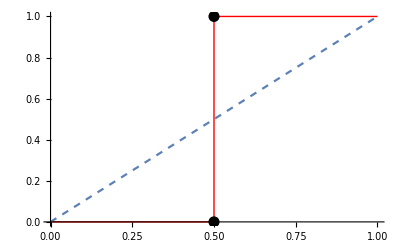

```mathematica
T=0.5;
p1={T,0};p2={T,1};
points={{0,0},p1,p2,{1,1}};
g1=ListPlot[points,Joined->True,PlotStyle->{Thick,Red}];
g2=Graphics[{PointSize[0.02],Point[{p1,p2}]}];
ref=Plot[x,{x,0,1},PlotStyle->Dashed];
Show[g1,g2,ref]
```

```mathematica
img=Import["lena_gray_256.tif"];
img2=Image[Map[Piecewise[{{0,#<=T},{1,#>T}}]&,ImageData[img],{2}]];
GraphicsRow[{img,img2}]
```

-Graphics-

```mathematica
ClearAll[r,g,b,colorLevel,x];
r[x_]:=Piecewise[{{0.1,0<=x<=0.2},{0.3,0.2<x<=0.4},{0.5,0.4<x<=0.6},{0.7,0.6<x<=0.8},{0.9,0.8<x<=1.0}}];
g[x_]:=Piecewise[{{0.8,0<=x<=0.2},{0.6,0.2<x<=0.4},{0.4,0.4<x<=0.6},{0.2,0.6<x<=0.8},{0,0.8<x<=1.0}}];
b[x_]:=Piecewise[{{0.2,0<=x<=0.2},{0.4,0.2<x<=0.4},{0.6,0.4<x<=0.6},{0.8,0.6<x<=0.8},{1.0,0.8<x<=1.0}}];
colorLevel[x_]:={r[x],g[x],b[x]};
```

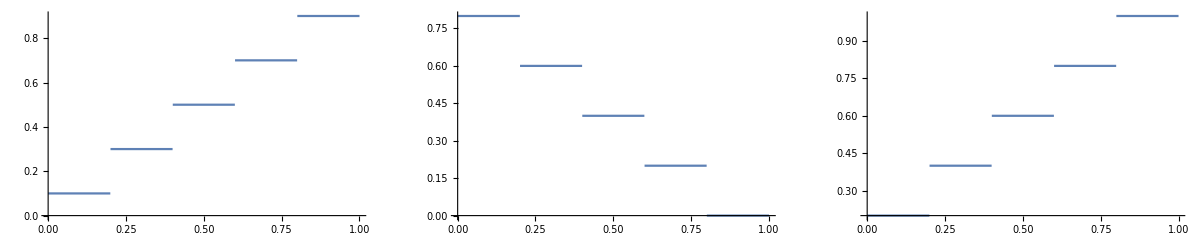

```mathematica
GraphicsRow[{Plot[r[x],{x,0,1}],Plot[g[x],{x,0,1}],Plot[b[x],{x,0,1}]}]
```

```mathematica
img=Import["Fig0304(a)(breast_digital_Xray).tif"];
img2=Image[Map[colorLevel,ImageData[img],{2}]];
GraphicsRow[{img,img2}]
```

-Graphics-

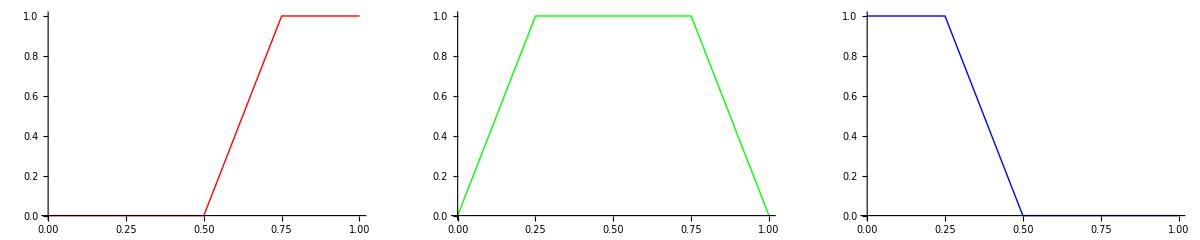

```mathematica
ClearAll[Lm,gr,gg,gb];
Lm=1;
gr=ListPlot[{{0,0},{Lm/2,0},{3Lm/4,Lm},{Lm,Lm}},Joined->True,PlotStyle->{Thick,Red}];
gg=ListPlot[{{0,0},{Lm/4,Lm},{3Lm/4,Lm},{Lm,0}},Joined->True,PlotStyle->{Thick,Green}];
gb=ListPlot[{{0,Lm},{Lm/4,Lm},{Lm/2,0},{Lm,0}},Joined->True,PlotStyle->{Thick,Blue}];
GraphicsRow[{gr,gg,gb}]
```

```mathematica
ClearAll[tab,x,piece];
line2point[x_,p1_,p2_]:=Module[{},(p2[[2]]-p1[[2]])/(p2[[1]]-p1[[1]])*(x-p1[[1]])+p1[[2]]];
Rx1=0.5;Rx2=0.75;
Ry1=0;Ry2=1;
r[t_]:=Module[{},Piecewise[
{{0,t≤Rx1},{1,t≥Rx2},{line2point[t,{Rx1,Ry1},{Rx2,Ry2}],Rx1<t<Rx2}}]
];
Gx1=0.25;Gx2=0.75;
Gy1=1;Gy2=1;
g[t_]:=Module[{},Piecewise[{{line2point[t,{0,0},{Gx1,Gy1}],t<Gx1},{1,Gx1≤t≤Gx2}},line2point[t,{Gx2,Gy2},{1,0}]]
];
Bx1=0.25;Bx2=.5;
By1=1;By2=0;
b[t_]:=Module[{},Piecewise[
{{1,t<Bx1},{0,t≥Bx2},{line2point[t,{Bx2,By2},{Bx1,By1}],Bx1<t<Bx2}}]
];
```

```mathematica
color[x_]:={r[x],g[x],b[x]};
img=Import["Fig0304(a)(breast_digital_Xray).tif"];
img2=Image[Map[color,ImageData[img],{2}]];
GraphicsRow[{img,img2}]
```

-Graphics-

2016/3/24